```mathematica
Vlj[R_,σ_] = 4*(  (σ/ R)^12 -  (σ/R)^6 )
```

4 (-σ^6/R^6+σ^12/R^12)

```mathematica
Vsmooth[b_,R_,rc_] =  b* (R-rc)^2
```

b (R-rc)^2

```mathematica
Clear[σ]
Clear[R]
D[Vlj[R,σ],R] 

Solve[{Vlj[R,σ] == Vsmooth[b,R,rc],
D[Vlj[R,σ],R] == D[Vsmooth[b,R,rc],R]},{b,rc}]
```

4 ((6 σ^6)/R^7-(12 σ^12)/R^13)

{{b→(36 σ^6 (-R^6+2 σ^6)^2)/(R^14 (-R^6+σ^6)),rc→(R (4 R^6-7 σ^6))/(3 (R^6-2 σ^6))}}

```mathematica
EXCVol[R_,b_,σ_,rc_,rstar_] = Piecewise[{ {Vlj[R,σ],R<rstar}, {Vsmooth[b,R,rc],rstar<R < rc},{0,R>rc}}]
```

Piecewise[{{4 (-σ^6/R^6+σ^12/R^12), R<rstar}, {b (R-rc)^2, rstar<R<rc}, {0, True}}]

```mathematica
Sigma is where potential should equal 0;
```

```mathematica
sol = {{b->(36 σ^6 (-R^6+2 σ^6)^2)/(R^14 (-R^6+σ^6)),rc->(R (4 R^6-7 σ^6))/(3 (R^6-2 σ^6))}} /. {σ->.75,R->.9 }
```

{{b→-2.44009,rc→1.50426}}

```mathematica
{{b->-2.4400937865209182,rc->1.50426457224458}}
```

{{b→-2.44009,rc→1.50426}}

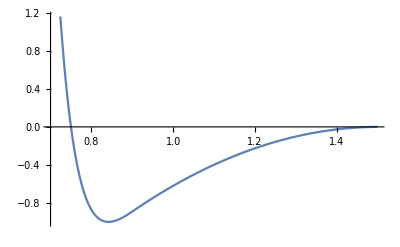

```mathematica
Plot[EXCVol[x,b,.75,rc,.9] /. sol,{x,.7,1.5}]
```